### CYCLE du moteur à 4 temps (cyle Otto)

REFERENCE:
THERMODYNAMIQUE,  Cengel, Bolles, Lacroix    
(Bibliothèqie cote 536 CENGE)

problème 9.33 page 455:

Rapport de compression : 9.5
Début de la compression adiabatique : V1= 6*10^-4  m^3  p1 =100 kPa  T1= 308 K
Fin de la détente adiabatique:  T4 = 800 K

air : gamma=1.4

### Coordonnées des points 1, 2, 3, 4 dans le cycle

```mathematica
v2=0.6316*10^-4;
v1=6*10^-4;
v3=v2;
v4=v1;
p1=10^5;
p2=2.338*10^6;
p3=p34[v2]
```

p34[0.00006316]

### Equations des adiabates

```mathematica
p12[v_]:=3.086/v^1.4
p34[v_]:=8.015/v^1.4
```

### Dessin des adiabates

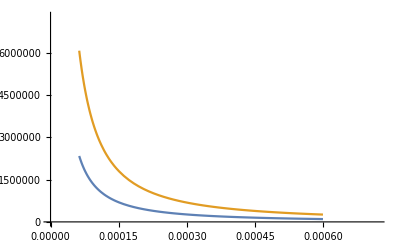

```mathematica
Plot[{p12[v],p34[v]},{v,v1,v2},PlotRange->{{0,1.2*v1},{0,1.2*p3}}]
```

### Intégrales de travail w(V)= ∫_(Volume initial)^V p(V)ⅆV

```mathematica
∫_(6*10^-4)^(0.6316*10^-4) p12[v]ⅆv
```

-219.118

```mathematica
∫_(0.6316*10^-4)^(6*10^-4) p34[v]ⅆv
```

569.097

### *****************

```mathematica
w34[x_]:=∫_(0.6316*10^-4)^x p34[v]ⅆv
```

```mathematica
w34[v1]   (*  contrôle  *)
```

569.097

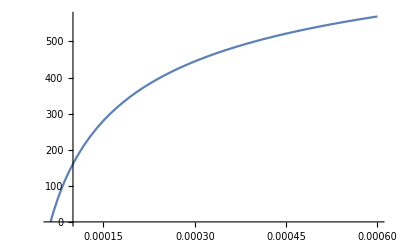

```mathematica
Plot[w34[x],{x,v3,v4}]
```

### *****************

```mathematica
w12[x_]:=∫_v1^x p12[v]ⅆv
```

```mathematica
w12[v2]      (*  contrôle  *)
```

-219.118

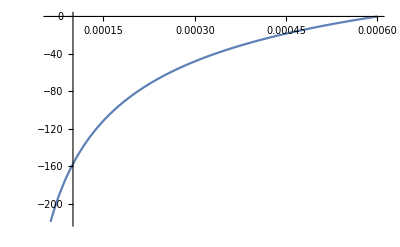

```mathematica
Plot[w12[x],{x,v1,v2}]    (*  CE GRAPHE SE LIT DE DROITE A GAUCHE   *)
```

### Calcul du rendement selon la définition: (Travail fourni)/(chaleur fournie Q23)

```mathematica
(∫_(0.6316*10^-4)^(6*10^-4) p34[v]ⅆv+∫_(6*10^-4)^(0.6316*10^-4) p12[v]ⅆv)*1/590
```

0.593184

### Calcul du rendement selon l’expression théorique

```mathematica
1-1/(v1/v2)^(1.4-1)
```

0.593635